## Plane Curves, Singularities and Resolutions

```mathematica
Needs["PlaneCurves`"]
```

## Local Study of Singularities

## Examples

### Double Line

```mathematica
SingularQ[x^2-y^2]
SingularPoints[x^2-y^2]
Map[PointM[x^2-y^2,#]&,SingularPoints[x^2-y^5]]
```

True

{{x→0,y→0}}

{2}

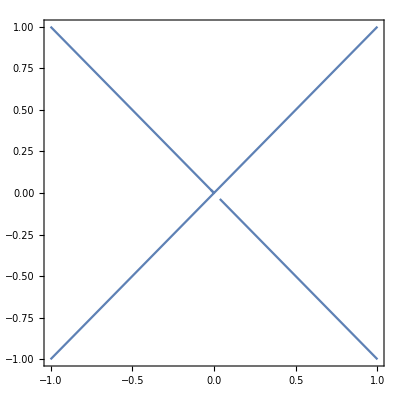

```mathematica
ContourPlot[x^2-y^2==0,{x,-1,1},{y,-1,1}]
```

```mathematica
ResolutionOfSingularities[x^2-y^2]
```

{{{1-v0^2,-1+v1^2},{x→0,y→0}}}

```mathematica
(*Since not irreducible, GeometricGenus won't return anything
GeometricGenus[x^2-y^2]*)
```

### Cuspidal Cubic

```mathematica
SingularQ[x^2-y^3]
SingularPoints[x^2-y^3]
Map[PointM[x^2-y^3,#]&,SingularPoints[x^2-y^3]]
```

True

{{x→0,y→0}}

{2}

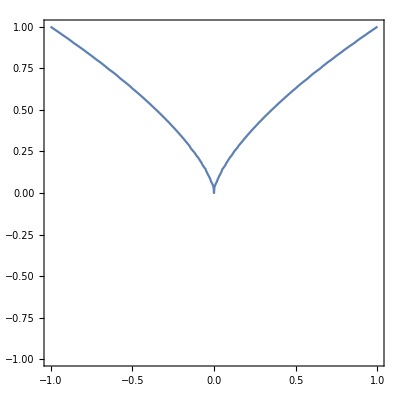

```mathematica
ContourPlot[x^2-y^3==0,{x,-1,1},{y,-1,1}]
```

```mathematica
ResolutionOfSingularities[x^2-y^3]
```

{{{1-u0 v0^3,-u1+v1^2},{x→0,y→0}}}

### Another Example

One singular point of multiplicity 2

```mathematica
SingularQ[x^2-y^5]
SingularPoints[x^2-y^5]
Map[PointM[x^2-y^5,#]&,SingularPoints[x^2-y^5]]
```

True

{{x→0,y→0}}

{2}

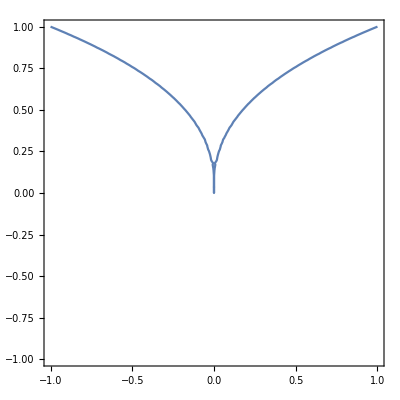

```mathematica
ContourPlot[x^2-y^5==0,{x,-1,1},{y,-1,1}]
```

```mathematica
ResolutionOfSingularities[x^2-y^5]
```

{{{1-u0^3 v0^5,-u10+v10^2,1-u11 v11^3},{x→0,y→0}}}

### Example: Smooth genus 3 curve

```mathematica
c1=1+x y+x^2+y^4+x^2+x^4;
SingularQ[c1]
```

False

```mathematica
Projectivize[c1,z]
GeometricGenus[c1]
```

x^4+y^4+2 x^2 z^2+x y z^2+z^4

3

### A-Polynomial Figure Eight

```mathematica
A41[x_,l_]:=x^2+l^2 x^2+l (-1+x+2 x^2+x^3-x^4)
```

It has two singular points of multiplicity 2

```mathematica
SingularQ[A41[x,l]]
SingularPoints[A41[x,l]]
Map[PointM[A41[x,l],#]&,SingularPoints[A41[x,l]]]
```

True

{{x→-1,l→1},{x→1,l→-1}}

{2,2}

Plot Imaginary parts

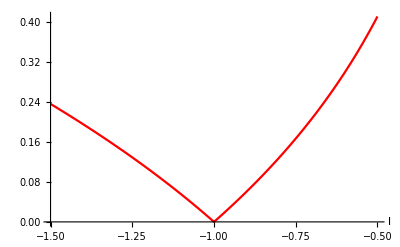

```mathematica
sol[l_]:=FindRoot[A41[x,l],{x,1+0.1*I}][[1,2]]
Plot[(*{Re[sol[l]],*)Im[sol[l]],{l,-0.5,-1.5},AxesLabel->{l,None},PlotLegends->"Expressions",PlotStyle->{Blue,Red}]
```

```mathematica
ResolutionOfSingularities[A41[x,l]]
```

{{{1-2 u0 v0-5 v0^2-5 u0 v0^2+u0^2 v0^2+5 u0 v0^3+5 u0^2 v0^3-u0^2 v0^4-u0^3 v0^4,-5+5 u1-u1^2-5 u1 v1+5 u1^2 v1-u1^3 v1+v1^2-2 u1 v1^2+u1^2 v1^2},{x→-1,l→1}},{{1+2 u0 v0+3 v0^2-3 u0 v0^2+u0^2 v0^2+3 u0 v0^3-3 u0^2 v0^3+u0^2 v0^4-u0^3 v0^4,3+3 u1+u1^2-3 u1 v1-3 u1^2 v1-u1^3 v1+v1^2+2 u1 v1^2+u1^2 v1^2},{x→1,l→-1}}}

```mathematica
(*This doesnt take into account points at infinity, so gives an incorrect genus*)
GeometricGenus[A41[x,l]]
```

4

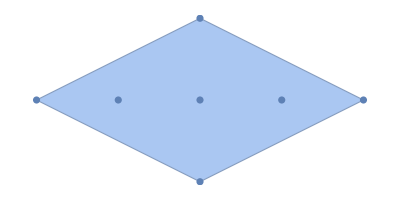

```mathematica
Show[ConvexHullMesh[NewtonPolygon[A41[x,l]]],ListPlot[NewtonPolygon[A41[x,l]]]]
```

## Points at infinity

```mathematica
A41[x_,l_]:=x^2+l^2 x^2+l (-1+x+2 x^2+x^3-x^4)
A41y[x_,z_]=Expand[A41[x/z,1/z]z^5];
A41x[y_,z_]=Expand[A41[1/z,y/z]z^5];
```

```mathematica
(*There is an extra singularity at y=Infinity*)
sing=SingularPoints[A41y[x,z]]
PointM[A41y[x,z],#]&/@sing
OrdinarySingularityQ[A41y[x,z],#]&/@sing
```

{{x→-1,z→-1},{x→0,z→0},{x→-1,z→1}}

{2,3,2}

{True,False,True}

## Global Properties (construction of 1-forms, fundamental differentials...)

```mathematica
(*Adjoint[]*)
(*Basis Cohomology*)
(*BranchNumber[poly_,{u_,v_}]:=*)
(*Branchpoints*)
(*Points at infinity*)
(*Fundamental objects*)
```

```mathematica
AsymptoticSolve[x x+y^5==0,{y,0},{x,0,4}]
AsymptoticSolve[x x+y^5==0,{x,0},{y,0,4}]
```

{{y→-x^(2/5)},{y→(-1)^(1/5) x^(2/5)},{y→-(-1)^(2/5) x^(2/5)},{y→(-1)^(3/5) x^(2/5)},{y→-(-1)^(4/5) x^(2/5)}}

{{x→-ⅈ y^(5/2)},{x→ⅈ y^(5/2)}}

```mathematica
ProjectiveSingularPoints[poly_]:=Join[SingularPoints[poly],Table[Module[{p=Expand[Projectivize[poly,z]/.{v->1}]},Solve[Join[Table[D[p,$v]==0,{$v,Variables[p]}],{p==0,==0}],Variables[p]]],{v,Variables[poly]}]]
```